```mathematica
SetDirectory[NotebookDirectory[]];
```

# Изучение особенностей возбуждения и распространения акустических волн СВЧ в твердых телах

## Выполнил : Нехаев Александр гр. 654

## Цель работы : Снять частоту, зависимость коэффициента затухания амплитуды. Определить константы упругости 2 - го порядка.

## Экспериментальная установка

## Ход работы

Сняли частотную зависимость α(v) в кристалле SiO_2.

```mathematica
data=Import["data.xlsx"][[1]];
data[[1,4]]="α";
data[[2;;7,1]]=Quantity[data[[2;;7,1]],"Megahertz"];
data[[2;;7,2]]=Quantity[data[[2;;7,2]],"Volts"];
data[[2;;7,3]]=Quantity[data[[2;;7,3]],"Volts"];data[[2;;7,4]]=Quantity[data[[2;;7,4]],1/"Centimeters"];
TableForm[data]
```

V, МГц | U1, В | U2, В | α
430. MHz | 1. V | 2.1 V | 0.555174 /cm
500. MHz | 3.4 V | 5. V | 0.288582 /cm
600. MHz | 3. V | 5.8 V | 0.493298 /cm
700. MHz | 2. V | 4.2 V | 0.555174 /cm
800. MHz | 1.6 V | 4. V | 0.685638 /cm
980. MHz | 0.8 V | 3.7 V | 1.14597 /cm

Полученная зависимость показана на графике.

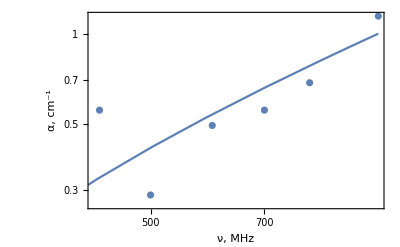

```mathematica
plotData=Transpose[{QuantityMagnitude[data[[2;;7,1]]],QuantityMagnitude[data[[2;;7,4]]]}];
plotApprox=LinearModelFit[plotData,x,x];
Show[
ListLogLogPlot[plotData,PlotTheme->"Detailed",FrameLabel->{"ν, MHz","α, cm^-1"}],
LogLogPlot[plotApprox["BestFit"],
{x,
Min[{plotData[[All,1]],plotData[[All,2]]}],
Max[{plotData[[All,1]],plotData[[All,2]]}]
}
]
]
```

Параметры образца:

```mathematica
L=Quantity[2.9, "Centimeters"];
t=Quantity[54/7,"Seconds"];
```

Проведем расчет Δ_диф на ν=400 MHz по формуле

Δ_диф=20*Log[(λ l)/(π a^2)]*(Sin[(λ l)/(π a^2)*π/3.83]^4)/(((λ l)/(π a^2)*π/3.83)^4);

Радиус преобразователя приближенно равен:

```mathematica
a=Quantity[0.05, "Centimeters"];
```

```mathematica
l=2 L;
```

λ_з - длина волны УЗВ:

```mathematica
Subscript[λ, з]=(l/t)/Quantity[400, "Megahertz"];
```

Тогда получаем:

```mathematica
Δдиф[λ_,l_,a_]:=20*Log[(λ l)/(π a^2)]*(Sin[(λ l)/(π a^2)*π/3.83]^4)/(((λ l)/(π a^2)*π/3.83)^4);
Δдиф[Subscript[λ, з],l,a]
```

-269.752

Определим скорость УЗВ в кристалле

```mathematica
v=(2L)/t
```

0.751852 cm/s

Считая, что мы измерили скорость продольной волны, вычислили один из коэффициентов тензора модулей упругости:

Значение плотности ρ для SiO_2:

```mathematica
ρ=ChemicalData["SiliconDioxide","Density"]
```

2196. kg/m^3

```mathematica
Subscript[c, 11]=ρ*v^2
```

0.124136 kg/(m s^2)

## Вывод

Сняли частотную характеристику коэффициента затухания амплитуды УЗВ в кристалле SiO_2. Определили скорость распространения УЗВ в кристалле SiO_2. Определили константу упругости 2-го порядка, оценили дифракционные потери в кристалле SiO_2.